```mathematica
(*Moments for m=inf*)

gaussianantenna=1;
α=2.;
alpha =α;
varphiRX = 0.0279;
thetaG = varphiRX;
h=1200.;
elevation =90.;
Kt=Ki=0;
ρ=Log[10.]/10;
μLoS=0*ρ;
μNLoS=-12*ρ;
σLoS=2.8*ρ;
σNLoS=9*ρ;
(*mLoS=ⅇ^(μLoS+σLoS^2/2);
mNLoS =ⅇ^(μNLoS+σNLoS^2/2);*)
mLoS=Sqrt[ⅇ^(2 μLoS+Abs[σLoS]^2) (-1+ⅇ^(Abs[σLoS]^2))];
mNLoS=Sqrt[ⅇ^(2 μNLoS+Abs[σNLoS]^2) (-1+ⅇ^(Abs[σNLoS]^2))];
β=2.3;
pLoS = Exp[-β*Cot[elevation/360.*2*Pi]];
shadowingprobability = 1-pLoS;
(*tildekappa*)
κ=1;
(*tildekappa*)
per3dB =κ*Log[2];
rE = 6378.;
r=Re[ArcCos[1/(2 (h+rE))(rE+rE Cos[(elevation π)/90]+√2 √(2 h^2+4 h rE+rE^2-rE^2 Cos[(elevation π)/90]) Sin[(elevation π)/180])]];

antennapattern[theta_] :=gaussantennapattern[theta,thetaG];
gammamax =ArcCos[rE/(rE+h)];
cutoff= findcutoff[r,h,thetaG] ; 
homocutoff= findcutoff[0,h,thetaG] ;
ah = ellipseparameters[r,h,thetaG][[1]];
Bh = ellipseparameters[r,h,thetaG][[2]];
ch = ellipseparameters[r,h,thetaG][[3]];
H =ellipseparameters[r,h,thetaG][[4]];

Cssim = ((-rE+(h+rE) Cos[r])/(h^2+2 h rE+2 rE^2-2 rE (h+rE) Cos[r]));
lambda = per3dB/(Pi*varphiRX^2*1/Cssim^2);

dens=lambda;
lambdaUE = lambda;

dsim=Sqrt[(Cos[r]*(rE+h)-rE)^2+(Sin[r]*(rE+h))^2];

csim[varphiRX_] := ((1/Cssim)^2 Pi*lambda varphiRX^2)/Log[2];
Cs = Sin[(elevation π)/180.]^2/h;
lambda = per3dB/(Pi*varphiRX^2*1/Cs^2);

d=h/Sin[(elevation π)/180.];
c[varphiRX_] := ((1/Cs)^2 Pi*lambda varphiRX^2)/Log[2];
noise= 1/d^alpha;

noise=0;


Moment1[varphiRX_]:=c[varphiRX]/d^α;
Moment2[varphiRX_] :=c[varphiRX]^2/d^(2*α) + 2*c[varphiRX]/(4*d^(2*α));
Moment1[varphiRX]
Moment2[varphiRX]
variance[varphiRX_] := Moment2[varphiRX]-Moment1[varphiRX]^2;
```

6.94444×10^-7

7.2338×10^-13

```mathematica
pc[θ_,κ_]:= NIntegrate[(κ*(pLoS))*Exp[-θ*v*noise*d^α/mLoS]/(v*(1+θ*v*mNLoS/mLoS)^(κ*(1-pLoS))*(1+θ*v)^(κ*pLoS))+(κ*(1-pLoS))*Exp[-θ*v*noise*d^α/mNLoS]/(v*(1+θ*v)^(κ*(1-pLoS))*(1+θ*v*mLoS/mNLoS)^(κ*pLoS)),{v,1,Infinity}];
averagepc[κ_]:=NIntegrate[(κ*(pLoS))*Exp[-θ*v*noise*d^α/mLoS]/(v*(1+θ*v*mNLoS/mLoS)^(κ*(1-pLoS))*(1+θ*v)^(κ*pLoS))+(κ*(1-pLoS))*Exp[-θ*v*noise*d^α/mNLoS]/(v*(1+θ*v)^(κ*(1-pLoS))*(1+θ*v*mLoS/mNLoS)^(κ*pLoS)),{v,1,Infinity},{θ,1,Infinity}];
bitratepc[κ_]:=1/Log[2]*NIntegrate[((κ*(pLoS))*Exp[-θ*v*noise*d^α/mLoS]/(v*(1+θ*v*mNLoS/mLoS)^(κ*(1-pLoS))*(1+θ*v)^(κ*pLoS))+(κ*(1-pLoS))*Exp[-θ*v*noise*d^α/mNLoS]/(v*(1+θ*v)^(κ*(1-pLoS))*(1+θ*v*mLoS/mNLoS)^(κ*pLoS)))/(θ+1),{v,1,Infinity},{θ,1,Infinity}];
stpc[θ_]:=θ^-κ*Hypergeometric2F1[κ,κ,κ+1,-1/θ];
```

```mathematica
pc[1,1.]
averagepc[2]
bitratepc[3]
```

0.7043

0.696157

0.0999887

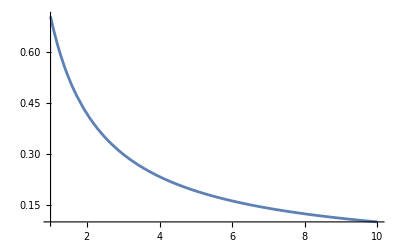

```mathematica
Plot[pc[θ,1.],{θ,1,10},PlotRange->Full]
```

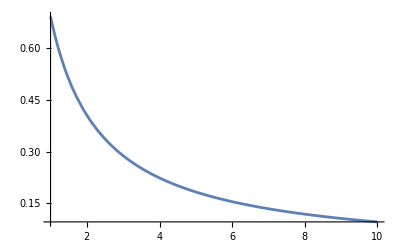

```mathematica
Plot[pc[θ,1.],{θ,1,10},PlotRange->Full]
```